# MÉTODOS COMPUTACIONALES EN ÓPTICA PROYECTO CONJUNTO MATHEMATICA-MATLAB

## Sistema láser bombeado ópticamente con dependencia espacial Realizado por Isabel Rodríguez y Javier Gil

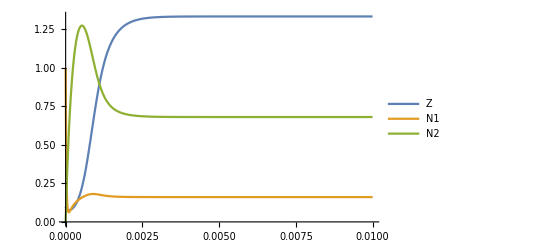

```mathematica
(* Simulamos un láser de Nd:YAG bombeado ópticamente*)
SetDirectory[NotebookDirectory[]];
(*Utilizamos como referencia las ecuaciones de la pág. 14 del Tema 5. Dinámica del láser de la asignatura Fundamentos de los láseres*)

(*Simulamos el caso de que el bombeo sea constante y no dependa de la posición*)
r=7000; (*Bombeo, luego se cambiará por un modo de Hermite-Gauss*)
trel21=230*10^-6;(* en segundos*)
trel10=23*10^-6;(*en segundos*)
lambda=1.06*10^-6;(*m*)
A21=1/trel21;
h=6.626*10^-34 ;(*J·s*)
c=3*10^8;(*m/s^2*)
g=100000;
B21=(lambda^3*A21)/(8*Pi*h);(*Coincide con el valor de la pág. 16 del Tema 4. Bases de la teoría láser*)
b21=B21*h*(c/lambda)*g ;(*Ecuación pág. 30 del Tema 4. Bases de la teoría láser*)
tp=3.3*10^-4;

(*Ecuaciones de balance pág. 14 del Tema 5. Dinámica del láser*)
sol:=NDSolve[{
N2'[t]== r-N2[t]/trel21-b21*Z[t]*(N2[t]-N1[t]),
N1'[t]== -N1[t]/trel10 +N2[t]/trel21+b21*Z[t]*(N2[t]-N1[t]),
Z'[t]==+b21*Z[t]*(N2[t]-N1[t])-Z[t]/tp,
N1[0]==1,
N2[0]==0,
Z[0]==0.1
}, {N1[t],N2[t],Z[t]}, {t,0,10}]

(*Extraemos las soluciones y las guardamos en variables para representarlas*)
solN1[t_]:=N1[t]/. sol[[1]];
solN2[t_]:=N2[t]/. sol[[1]];
solZ[t_]:=Z[t]/. sol[[1]];

(*Las representamos*)
Plot[Evaluate[{solZ[t],solN1[t],solN2[t]}],{t,0,10^-2},PlotRange->All,PlotLegends->{"Z","N1","N2"}]
```

```mathematica
(*Modos gaussianos de Hermite gauss que serán nuestro bombeo*)
(*Para que no dependan de z, ponemos el haz en el foco z=0*)
 f[n_,x_]:=√(1/(2^n n!))HermiteH[n,√2 x] E^(-x^2); 
Intensity[m_,n_,x_,y_]:=f[m,x]^2 f[n,y]^2 ;(* Definimos la intensidad, que es lo que vamos a representar *)
(* Definimos la función bombeo dependiente de la intensidad y la multiplico por un número lo suficientemente grande como para que el bombeo sea percibido por el sistema *)
r1[m_,n_,x_,y_]:=Intensity[m,n,x,y]*(70000/4) (*Este factor nos permite reproducir la anterior evolución del sistema que hemos graficado*)
m=0;
n=4;
Plot3D[r1[m,n,x,y],{x,-5,5},{y,-5,5},PlotRange->All,ColorFunction->"TemperatureMap"]
(*Representamos el bombeo en función de los distintos modos gaussianos *)
```

-Graphics3D-

```mathematica
(*Ecuaciones de balance con dependencia espacial y temporal*)
resol[x_,y_]:=NDSolve[{
Nd2'[t]== r1[m,n,x,y]-Nd2[t]/trel21-b21*Zd[t]*(Nd2[t]-Nd1[t]),
Nd1'[t]== -Nd1[t]/trel10 +Nd2[t]/trel21+b21*Zd[t]*(Nd2[t]-Nd1[t]),
Zd'[t]==+b21*Zd[t]*(Nd2[t]-Nd1[t])-Zd[t]/tp,
Nd1[0]==1,
Nd2[0]==0,
Zd[0]==0.5
}, {Nd1,Nd2,Zd}, {t,0,10}]

(*Extraemos las soluciones*)
resolNd1[t_,x_,y_]:=Nd1[t]/. resol[x,y][[1]];
resolNd2[t_,x_,y_]:=Nd2[t]/. resol[x,y][[1]];
resolZd[t_,x_,y_]:=Zd[t]/. resol[x,y][[1]];

(*Damos valor a las soluciones en diferentes instantes*)
```

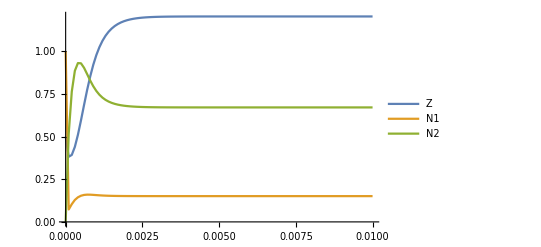

```mathematica
densitifoton=Table[{t1,resolZd[t1,0,0]},{t1,0,10^-2,10^-4}];
nivel01=Table[{t1,resolNd1[t1,0,0]},{t1,0,10^-2,10^-4}];
nivel02=Table[{t1,resolNd2[t1,0,0]},{t1,0,10^-2,10^-4}];
(*Las representamos*)
AAA=ListPlot[{densitifoton,nivel01,nivel02},PlotRange->All,Joined->True,PlotLegends->{"Z","N1","N2"}]
```

```mathematica
(*OJO: Esta parte tarda en compilar*)
(*Guardamos los valores para distintas posiciones espaciales y temporal del nivel1,2 y la densidad de fotones*)
nivel1=Table[{t1,x1,y1,resolNd1[t1,x1,y1]},{t1,0,10^-2,5*10^-4},{x1,-5,5,0.2},{y1,-5,5,0.2}];
nivel2=Table[{t1,x1,y1,resolNd2[t1,x1,y1]},{t1,0,10^-2,5*10^-4},{x1,-5,5,0.2},{y1,-5,5,0.2}];
densityfoton1=Table[{t1,x1,y1,resolZd[t1,x1,y1]},{t1,0,10^-2,5*10^-4},{x1,-5,5,0.2},{y1,-5,5,0.2}];
```

```mathematica
(*OJO: Esta parte tarda en compilar*)
(*Representamos los valores con un densityplot*)
ListDensityPlot3D[Flatten[nivel1,2],ColorFunction->"BlueGreenYellow",PlotRange->All,PlotLegends->Automatic]
ListDensityPlot3D[Flatten[nivel2,2],ColorFunction->"BlueGreenYellow",PlotRange->All,PlotLegends->Automatic]
ListDensityPlot3D[Flatten[densityfoton1,2],ColorFunction->"BlueGreenYellow",PlotRange->All,PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*Ficheros que exportamos a MATLAB*)
(*Hacemos un table que vaya barriendo distintas posiciones de x e y*)
(*El for barre en el tiempo, cada iteración es un frame*)
(*Cada frame es un instante temporal en el que hay distintos valores de x e y guardados*)
densitifotonmat[h_]:=Table[{x1,y1,resolZd[2*h*10^-4,x1,y1]},{x1,-5,5,0.2},{y1,-5,5,0.2}];
For[i=0,i<10,i++,Export[StringJoin["frame",TextString[i+1],".dat"],Flatten[densitifotonmat[i],1]]];
(*La idea de que se generen automáticamente los archivos sin tener que escribirlos la sacamos de:
https://mathematica.stackexchange.com/questions/73135/how-to-change-the-name-of-exporting-file-automatically*)
```

```mathematica
(*Análogo que es caso anterior*)
nivel1mat[h_]:=Table[{x1,y1,resolNd1[h*10^-5,x1,y1]},{x1,-5,5,0.2},{y1,-5,5,0.2}];
For[i=0,i<16,i++,Export[StringJoin["nivel1",TextString[i+1],".dat"],Flatten[nivel1mat[i],1]]];
```

```mathematica
(*Análogo que es caso anterior*)
nivel2mat[h_]:=Table[{x1,y1,resolNd2[h*10^-4,x1,y1]},{x1,-5,5,0.2},{y1,-5,5,0.2}];
For[i=0,i<20,i++,Export[StringJoin["nivel2",TextString[i+1],".dat"],Flatten[nivel2mat[i],1]]];
```